```mathematica
(* Stage-Structure and Disease: DD maturation and juvenile disease *)
beta[b_]:=b;(*Beta as a function so that solutions can be plotted later as a function of b*)

eqJS:=JS'[t]==f*A[t]-uJ*JS[t]-(mo-mb*(JS[t]+JI[t]))*JS[t]-beta[b]*JS[t]*JI[t]; (*susceptible juvenile growth rate*)

eqJI:=JI'[t]==beta[b]*JS[t]*JI[t] -(uJ+a)*JI[t]; (*infectious juvenile growth rate*)

eqA:=A'[t]==(mo-mb*(JS[t]+JI[t]))*JS[t]-uA*A[t]; (*adult growth rate*)

eqsol=Solve[{eqJS[[2]]==0,eqJI[[2]]==0,eqA[[2]]==0},{JS[t],JI[t],A[t] }];(*steady state solutions, set derivative = 0 and solve*)
	(*eqR[[2]] is shorthand to grab the right hand side of the eq*)

eigenvals=Eigenvalues[{{D[eqJS[[2]],JS[t]],D[eqJS[[2]],JI[t]],D[eqJS[[2]],A[t]]},{D[eqJI[[2]],JS[t]],D[eqJI[[2]],JI[t]],D[eqJI[[2]],A[t]]},{D[eqA[[2]],JS[t]],D[eqA[[2]],JI[t]],D[eqA[[2]],A[t]]}}] ;(*determine if the steady state is stable against small perturbations (stability)*)
```

SetDelayed::write: Tag Real in 0.188[b_] is Protected.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
eqsol
```

{{JS[t]→0,JI[t]→0,A[t]→0},{JS[t]→(a+uJ)/b,JI[t]→(-a f mb+b f mo+a mb uA-b mo uA-f mb uJ-b uA uJ+mb uA uJ)/(b (f mb+b uA-mb uA)),A[t]→-((a mb-b mo) (a+uJ))/(b (f mb+b uA-mb uA))},{JS[t]→(f mo-mo uA-uA uJ)/(mb (f-uA)),JI[t]→0,A[t]→(uJ (f mo-mo uA-uA uJ))/(mb (f-uA)^2)}}

```mathematica
(*parameters*)
f=3;
uJ=0.5;
mo=2.5;
mb=0.2;
a=0.5;
uA=0.5;
```

```mathematica
(* Plot eigenvalues for the second solution (in which disease invasion occurs); plot real parts in solid, imaginary parts in dashed *)
Show[Plot[Re[Evaluate[eigenvals/.eqsol[[2]]]],{b,0.1,0.3}],
Plot[Im[Evaluate[eigenvals/.eqsol[[2]]]],{b,0.1,0.3},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
ReImPlot[Evaluate[eigenvals/.eqsol[[2]],{b,0,0.3}],PlotLegends->Automatic]
Plot[Max[Re[Evaluate[eigenvals/.eqsol[[2]]]]],{b,0,0.3}]
ReImPlot[Evaluate[eigenvals/.eqsol[[3]],{b,0,0.3}],PlotLegends->Automatic]
Plot[Max[Re[Evaluate[eigenvals/.eqsol[[3]]]]],{b,0,0.3}]
```

ReImPlot[{Root[6.-72. 0.188[0.2]+(4.7+15.6 0.188[0.2]) #1+(-0.3-12. 0.188[0.2]) #1^2+#1^3&,1],Root[6.-72. 0.188[0.2]+(4.7+15.6 0.188[0.2]) #1+(-0.3-12. 0.188[0.2]) #1^2+#1^3&,2],Root[6.-72. 0.188[0.2]+(4.7+15.6 0.188[0.2]) #1+(-0.3-12. 0.188[0.2]) #1^2+#1^3&,3]},{0.2,0,0.3},PlotLegends→Automatic]

-Graphics-

ReImPlot[{Root[0.+5.5/(1.+0.188[0.2])-0.5/(0.188[0.2] (1.+0.188[0.2]))+(6. 0.188[0.2])/(1.+0.188[0.2])+(-6.+1./(0.188[0.2])+2.1/(1.+0.188[0.2])-0.3/(0.188[0.2] (1.+0.188[0.2]))+(18. 0.188[0.2])/(1.+0.188[0.2])) #1+(3.5-0.4/(0.188[0.2])-3.4/(1.+0.188[0.2])+0.2/(0.188[0.2] (1.+0.188[0.2]))+(12. 0.188[0.2])/(1.+0.188[0.2])) #1^2+#1^3&,1],Root[0.+5.5/(1.+0.188[0.2])-0.5/(0.188[0.2] (1.+0.188[0.2]))+(6. 0.188[0.2])/(1.+0.188[0.2])+(-6.+1./(0.188[0.2])+2.1/(1.+0.188[0.2])-0.3/(0.188[0.2] (1.+0.188[0.2]))+(18. 0.188[0.2])/(1.+0.188[0.2])) #1+(3.5-0.4/(0.188[0.2])-3.4/(1.+0.188[0.2])+0.2/(0.188[0.2] (1.+0.188[0.2]))+(12. 0.188[0.2])/(1.+0.188[0.2])) #1^2+#1^3&,2],Root[0.+5.5/(1.+0.188[0.2])-0.5/(0.188[0.2] (1.+0.188[0.2]))+(6. 0.188[0.2])/(1.+0.188[0.2])+(-6.+1./(0.188[0.2])+2.1/(1.+0.188[0.2])-0.3/(0.188[0.2] (1.+0.188[0.2]))+(18. 0.188[0.2])/(1.+0.188[0.2])) #1+(3.5-0.4/(0.188[0.2])-3.4/(1.+0.188[0.2])+0.2/(0.188[0.2] (1.+0.188[0.2]))+(12. 0.188[0.2])/(1.+0.188[0.2])) #1^2+#1^3&,3]},{0.2,0,0.3},PlotLegends→Automatic]

-Graphics-

```mathematica
b=0.2;
Max[Re[Evaluate[eigenvals/.eqsol[[2]]]]]
```

-0.0272358

```mathematica
Select[Evaluate[eigenvals/.eqsol[[2]]],Re[Evaluate[eigenvals/.eqsol[[2]]]]==Max[Re[Evaluate[eigenvals/.eqsol[[2]]]]]]
```

{}

```mathematica
Re[Evaluate[eigenvals/.eqsol[[2]]]]
Max[Re[Evaluate[eigenvals/.eqsol[[2]]]]]
Re[Evaluate[eigenvals/.eqsol[[2]]]]==Max[Re[Evaluate[eigenvals/.eqsol[[2]]]]]
```

{-1.44553,-0.0272358,-0.0272358}

-0.0272358

{-1.44553,-0.0272358,-0.0272358}==-0.0272358

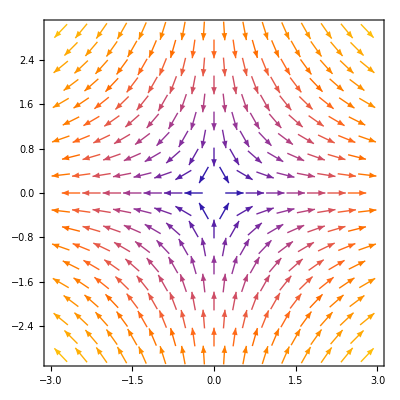

```mathematica
VectorPlot[{x,-y},{x,-3,3},{y,-3,3}]
```

```mathematica
eqJS:=JS'[t]==f*A[t]-uJ*JS[t]-(mo-mb*(JS[t]+JI[t]))*JS[t]-beta[b]*JS[t]*JI[t]; (*susceptible juvenile growth rate*)

eqJI:=JI'[t]==beta[b]*JS[t]*JI[t] -(uJ+a)*JI[t]; (*infectious juvenile growth rate*)

eqA:=A'[t]==(mo-mb*(JS[t]+JI[t]))*JS[t]-uA*A[t]; (*adult growth rate*)
```

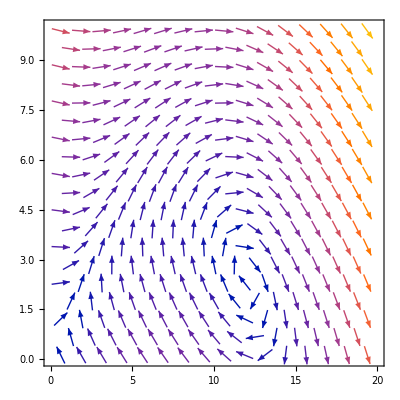

Point[12.,2.4]

```mathematica
VectorPlot[{f*A-uJ*JS-(mo-mb*(JS))*JS,(mo-mb*(JS))*JS-uA*A},{JS,0,20},{A,0,10}]

Point[eqsol[[3]][[1]][[2]],eqsol[[3]][[3]][[2]]]
```